# Lucrare de laborator n.3 PSA Popa Catalin TI-211 V-18

```mathematica
1. Este data repartitia v.a.d  de tip discret ξ:
```

```mathematica
ξ:({{x1, x2, x3, x4}, {p1, p2, p3, p4}})
```

Se cere:
	1) Sa se introduca in sistemul Mathematica repartitia v.a.ξ; 
	2) Functia de repartitie si graficul ei;
	3) Probabilitatea ca ξ va lua valori din intervalul [1;3];
	4) Valoarea medie;
	5) Dispersia;
	6) Abaterea medie patratica;
	7) Momentele initiale de ordine pana la 4 inclusiv;
	8) Momentele centrate de ordine pana la 4 inclusiv;
	9) Asimetria;
	10) Excesul.

```mathematica
1.
```

Introducem repartitia:

```mathematica
ξ = {{-1,0,1,2},{0.1,0.5,0.3,0.1}}
```

{{-1,0,1,2},{0.1,0.5,0.3,0.1}}

```mathematica
MatrixForm[ξ]
```

(-1 | 0 | 1 | 2
0.1 | 0.5 | 0.3 | 0.1)

2.Gasim functia de repartitie:

```mathematica
F[x_]:=0/;x<-1
```

```mathematica
F[x_]:=0.1/;-1≤x<-0
```

```mathematica
F[x_]:=0.6/;0≤x<1
```

```mathematica
F[x_]:=0.9/;1≤x<2
```

```mathematica
F[x_]:=1/;2≤x
```

4.Construim graficul:

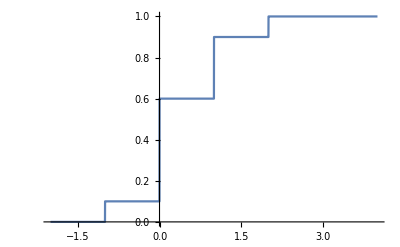

```mathematica
Plot[F[x],{x,-2,4}]
```

5.Determinam probabilitatea ca functia va lua valori in intervalul [1;4);

```mathematica
F(1≤ξ<4)=F[4]-F[1]
```

Set::write: Tag Times in F\ (1 ≤ {{-1, 0, 1, 2}, {0.1, 0.5, 0.3, 0.1}} < 4) is Protected.

0.1

```mathematica
Clear[F]
```

6)Calculam valoara medie:

```mathematica
Subscript[m, ξ]=∑_(j=1)^4 ξ[[1,j]]× ξ[[2,j]]
```

0.4

7)Calculam dispersia:

```mathematica
Subscript[D, ξ]=∑_(i=1)^4 (ξ[[1,i]]-Subscript[m, ξ])^2 ξ[[2,i]]
```

0.64

8)Calculam abaterea media patratica:

```mathematica
Subscript[σ, ξ]=√Subscript[D, ξ]
```

0.8

9)Calculam momentele initiale:

```mathematica
Subscript[α, 1]=∑_(i=1)^4 (ξ[[1,i]])^1 ξ[[2,i]]
```

0.4

```mathematica
Subscript[α, 2]=∑_(i=1)^4 (ξ[[1,i]])^2 ξ[[2,i]]
```

0.8

```mathematica
Subscript[α, 3]=∑_(i=1)^4 (ξ[[1,i]])^3 ξ[[2,i]]
```

1.

```mathematica
Subscript[α, 4]=∑_(i=1)^4 (ξ[[1,i]])^4 ξ[[2,i]]
```

2.

10)Calculam momentele centrate:

```mathematica
Subscript[μ, 1]=∑_(i=1)^4 (ξ[[1,i]]-Subscript[m, ξ])^1 ξ[[2,i]]
```

5.55112×10^-17

```mathematica
Subscript[μ, 2]=∑_(i=1)^4 (ξ[[1,i]]-Subscript[m, ξ])^2 ξ[[2,i]]
```

0.64

```mathematica
Subscript[μ, 3]=∑_(i=1)^4 (ξ[[1,i]]-Subscript[m, ξ])^3 ξ[[2,i]]
```

0.168

```mathematica
Subscript[μ, 4]=∑_(i=1)^4 (ξ[[1,i]]-Subscript[m, ξ])^4 ξ[[2,i]]
```

1.0912

11)Calculam asimetria:

```mathematica
Sk[ξ]=Subscript[μ, 3]/Subscript[σ, ξ]^3
```

0.328125

12)Calculam excesul:

```mathematica
Ex[ξ]=Subscript[μ, 4]/Subscript[σ, ξ]^4-3
```

-0.335938

Exercitiul 2.
Presupunem că probabilitatea statistică că un copil nou născut să fie băiat este egală cu 0.51. Se cere:
1) să se determine repartiţia v.a.  care reprezintă numărul de băieţi printre 1000 de copii noi născuţi; 2) să
se calculeze probabilitatea că printre 1000 de copii noi născuţi numărul băieţilor va fi cuprims între 300+k
şi 500+k, unde k este numărul variantei

1)

```mathematica
(1000!)/((18!)×((1000-18))!)*((0.51)^18)×((0.49)^(1000-18))
```

4.3215×10^-272

2)

```mathematica
N[∑_(k=300+18)^(500+18) ((1000!)/(k!*(1000-k)!)(0.51)^k(0.49)^(1000-k))]
```

0.704543

Exercitiul 3.
-Graphics-

```mathematica
evenA=∑_(k=0)^2 (1+18*0.25)^k/(k!)ⅇ^-2//N
```

2.92663

```mathematica
evenB=(1+18*0.25)^5/(5!)ⅇ^-2//N
```

5.67601

```mathematica
evenC=1-∑_(k=0)^10 (1+18*0.25)^k/(k!)ⅇ^-2//N
```

-31.2792

```mathematica
(1+18*0.25)^1/(1!)ⅇ^-2//N
```

0.744344

```mathematica
(1+18*0.25)^2/(2!)ⅇ^-2//N
```

2.04695

```mathematica
(1+18*0.25)^3/(3!)ⅇ^-2
```

3.75273

```mathematica
(1+18*0.25)^4/(4!)ⅇ^-2
```

5.16001

Cand numarul de particule α=4 , probabilitatea este maxima.
Exercitiul 4

-Graphics-

```mathematica
∑_(k=5+18)^(15+18) (5/6)^k*1/6//N
```

0.0130633

Exercitiul 5
-Graphics-
-Graphics-

```mathematica
F[x_]:=0/;x<3;
F[x_]:=(x-3)/8/;3≤x≤7;
F[x_]:=0/;x>7;
```

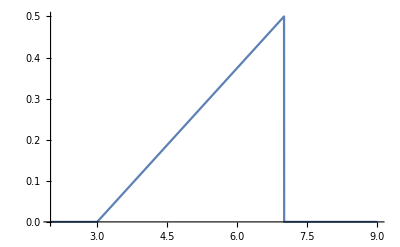

```mathematica
Plot[F[x],{x,2,9}]
```

```mathematica
F1[x]=∫_1^x (t-3)/8 ⅆt
```

5/16-(3 x)/8+x^2/16

```mathematica
F[x_]:=0/;x<3;F[x_]:=5/16-(3x)/8+x^2/16/;3≤x≤7;F[x_]:=1/;x>7;
```

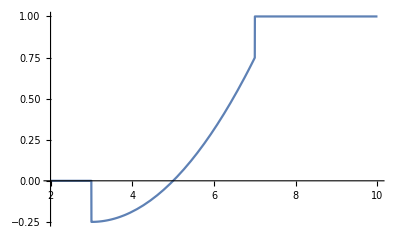

```mathematica
Plot[F[x],{x,2,10}]
```

```mathematica
medi=NIntegrate[x*F[x],{x,3,7}]
```

3.

```mathematica
dis=N[∫_3^7 (x-medi)^2 F[x]ⅆx]
```

7.46667

```mathematica
aba=Sqrt[dis]
```

2.73252

```mathematica
a1=medi
```

3.

```mathematica
a2=N[∫_3^7 x^2 F[x]ⅆx]
```

22.4667

```mathematica
a3=N[∫_3^7 x^3 F[x]ⅆx]
```

156.867

```mathematica
a4=N[∫_3^7 x^4 F[x]ⅆx]
```

1061.29

```mathematica
momc1=0
```

0

```mathematica
momc2=dis
```

7.46667

```mathematica
momc3=N[∫_3^7 (x-medi)^3 F[x]ⅆx]
```

26.6667

```mathematica
momc4=N[∫_3^7 (x-medi)^4 F[x]ⅆx]
```

95.0857

```mathematica
asimetria=momc3/aba^3
```

1.30701

```mathematica
exces=momc4/(aba^4-3)
```

1.80253

```mathematica
prob=aba/medi
```

0.91084

```mathematica
ClearAll
```

ClearAll

Exercitiul 6
18)m=8, σ=4, α=5, δ=9;

```mathematica
nd=NormalDistribution[8,4]
```

NormalDistribution[8,4]

```mathematica
defrep=PDF[nd,x]
```

(ⅇ^(-1/32 (-8+x)^2))/(4 √(2 π))

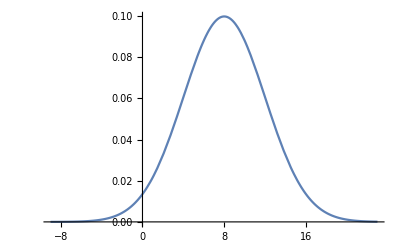

```mathematica
Plot[defrep,{x,-9,23}]
```

```mathematica
funrep=CDF[nd,x]
```

1/2 Erfc[(8-x)/(4 √2)]

Graficul functiei de repartitie

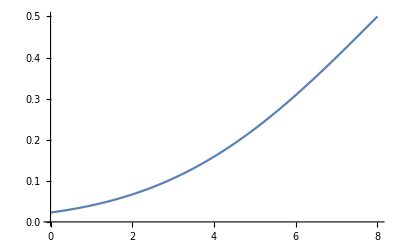

```mathematica
Plot[funrep,{x,0,8}]
```

graficele densităţii de repartiţie şi al funcţiei de repartiţie

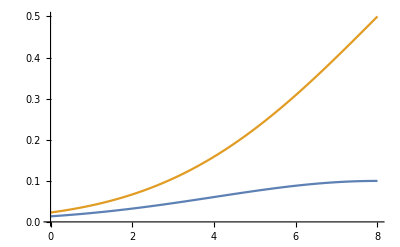

```mathematica
Plot[{defrep,funrep},{x,0,8}]
```

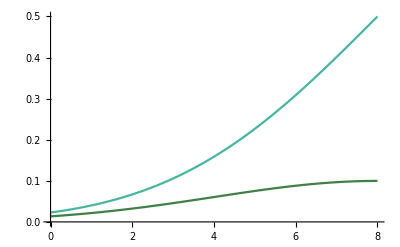

```mathematica
Plot[{defrep,funrep},{x,0,8},PlotStyle->{Hue[0.35,0.5,0.5],Hue[0.47,0.6,0.71]}]
```

```mathematica
Clear[nd,defrep,funrep]
```

Exercitiul 7

```mathematica
nd=NormalDistribution[175+(-1)^18/18,6-(-1)^18/18]
```

NormalDistribution[3151/18,107/18]

```mathematica
defrep=PDF[nd,x]
```

9/107 ⅇ^(-(162 (-3151/18+x)^2)/11449) √(2/π)

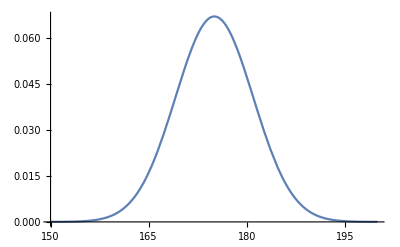

```mathematica
Plot[defrep,{x,150,200}]
```

```mathematica
N[∫_150^155 defrepⅆx]
```

0.000358157

```mathematica
N[∫_155^160 defrepⅆx]
```

0.00528857

```mathematica
N[∫_160^165 defrepⅆx]
```

0.039703

```mathematica
N[∫_165^170 defrepⅆx]
```

0.15217

```mathematica
N[∫_170^175 defrepⅆx]
```

0.298739

```mathematica
N[∫_175^180 defrepⅆx]
```

0.300961

```mathematica
N[∫_180^185 defrepⅆx]
```

0.155594

```mathematica
N[∫_185^190 defrepⅆx]
```

0.0412056

```mathematica
N[∫_190^195 defrepⅆx]
```

0.00557158

```mathematica
N[∫_195^200 defrepⅆx]
```

0.000383056

```mathematica
ClearAll
```

ClearAll

```mathematica
Clear
```

Clear

Exercitiul 8
Introducem d.r

```mathematica
f[x_]:=5*e^(-5x)/;x>0;
```

```mathematica
f[x_]:=0/;x<0;
```

Functia de repartitie

```mathematica
F[x_]:=1-e^(-5x)/;x≥0;
F[x_]:=0/;x<0;
```

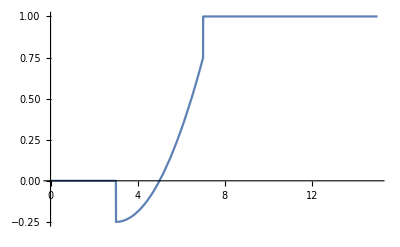

```mathematica
Plot[F[x],{x,0,15}]
```

Probabilitatea ca o sa asteptam nu mai mult de 2+n/3, n=18

```mathematica
P=e^(-5*(2+18/3))
```

1/e^40

Exercitiul 10

```mathematica
rn=NormalDistribution[500,150]
```

NormalDistribution[500,150]

```mathematica
drn=PDF[rn,x]
```

(ⅇ^(-(-500+x)^2/45000))/(150 √(2 π))

```mathematica
N[∫_(400+5*18)^(500+5*18) drnⅆx]
```

0.252323

```mathematica
p=N[∫_0^300 drnⅆx]
```

0.0907822

```mathematica
(10!)/(8!*(10-8)!)*p^2*(1-p)^8
```

0.173204